```mathematica
m = 0.44; 
g = 9.8; 
k1 = 0.0123; 
k2 = 0.0144;
ω0=15;
ω={0,0,ω0-t};
r[t_]:={x[t],y[t],z[t]};
v=r'[t];
G={0, 0, -m g};
fg=-k1 Norm[v]v;
fM = k2 ω×v;
eqns := m D[r[t], {t,2}]==G+fg+fM;
sol = NDSolveValue[{eqns,r[0]=={0, 0, 0},r'[0]=={24, 16, 8.5}},{x[t], y[t], z[t]},{t,0,30}]
ParametricPlot3D[sol, {t, 0, 20},PlotRange->300]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

-Graphics3D-

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2) (1-r Cos[θ])+(1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2) (1-r Cos[θ]) 得到非数值.

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (-1/2+z) Cos[θ] (1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2)+(1/2+z) Cos[θ] (1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

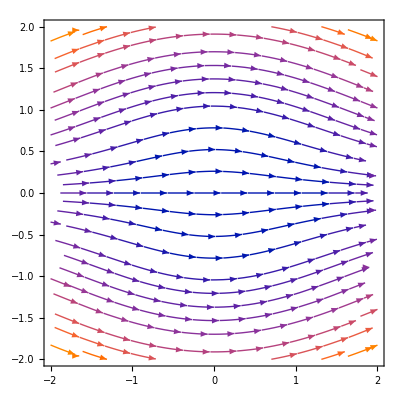

```mathematica
StreamPlot[{NIntegrate[(1-r Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(-3/2))+(1-r Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(-3/2)),{θ,0,2 π}],NIntegrate[((-1/2+z) Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(-3/2))+((1/2+z) Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(-3/2)),{θ,0,2 π}]},{z,-2,2},{r,-2,2}]
```

```mathematica
Plot3D[{NIntegrate[(1-r Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(-3/2))+(1-r Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(-3/2)),{θ,0,2 π}],NIntegrate[((-1/2+z) Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(-3/2))+((1/2+z) Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(-3/2)),{θ,0,2 π}]},{z,-2,2},{r,-2,2}]
```

-Graphics3D-

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (1-r Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2))+(1-r Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2)) 得到非数值.

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 ((-1/2+z) Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2))+((1/2+z) Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2)) 得到非数值.

NIntegrate::inumr: 在以 {{0,6.28319}} 为界的区域内，对于所有采样点，计算被积函数 (1-r Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2))+(1-r Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2)) 得到非数值.

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

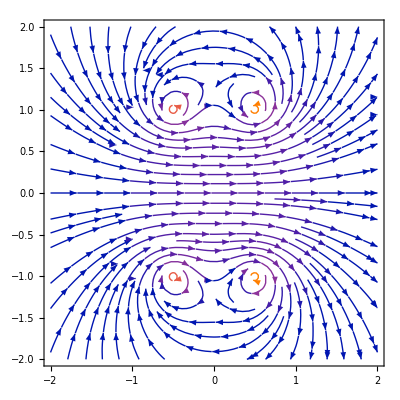

```mathematica
StreamPlot[Evaluate@{NIntegrate[(1-r Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2))+(1-r Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2)),{θ,0,2 π}],NIntegrate[((-1/2+z) Cos[θ])/((1+r^2+(-1/2+z)^2-2 r Cos[θ])^(3/2))+((1/2+z) Cos[θ])/((1+r^2+(1/2+z)^2-2 r Cos[θ])^(3/2)),{θ,0,2 π}]},{z,-2,2},{r,-2,2}]
```